## Core parameters

```mathematica
α=0.8;β=2;γ=.;u=0;
q1=2;q2=2.5;q3=3;
p[γ_,y_,q_]:=(1-γ)q/(q1+q2+q3)+α γ (y^β/(y^β+(1-y)^β));
```

```mathematica
cols=ColorData[97,"ColorList"]⟦{2,1,3}⟧
```

{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885]}

## Dynamic γ

```mathematica
G=0.1;
```

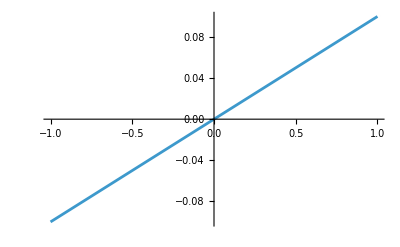

```mathematica
Plot[G y,{y,-1,1}]
```

```mathematica
dy1[y1_,y2_,γ_]:=y1((p[γ,y1,q1] q1-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))));
dy2[y1_,y2_,γ_]:=y2 ((p[γ,y2,q2] q2-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))));
```

```mathematica
sol[{y1init_,y2init_},Gon_]:=NDSolve[{y1'[t]==dy1[y1[t],y2[t],g[t]],y2'[t]==dy2[y1[t],y2[t],g[t]],(*g evolves according to dg*)g'[t]==If[Gon==True, G Sign[dy1[y1[t],y2[t],g[t]]],G],(*initial conditions*)y1[0]==y1init,y2[0]==y2init,g[0]==0.4},{y1,y2,g},{t,0,100}];
```

```mathematica
inits={};
Table[If[i+j<1,AppendTo[inits,{i,j}]],{i,0.1,1,0.1},{j,0.1,1,0.1}];
```

```mathematica
trajectoriesoff=Table[Table[Evaluate[{y1[t],1-y1[t]-y2[t],y2[t]}/.sol[inits[[j]],False]⟦1⟧],{t,0,100,0.05}],{j,1,Length[inits],1}];
trajectorieson=Table[Table[Evaluate[{y1[t],1-y1[t]-y2[t],y2[t]}/.sol[inits[[j]],True]⟦1⟧],{t,0,100,0.05}],{j,1,Length[inits],1}];
```

```mathematica
tolerance=0.01;
fixcolours[traj_]:=Table[
If[
AllTrue[Thread[Abs[Chop[Last[traj⟦i⟧]]-{1,0,0}]<tolerance],TrueQ],cols⟦1⟧,
If[AllTrue[Thread[Abs[Chop[Last[traj⟦i⟧]]-{0,1,0}]<tolerance],TrueQ],cols⟦3⟧,
If[AllTrue[Thread[Abs[Chop[Last[traj⟦i⟧]]-{0,0,1}]<tolerance],TrueQ],cols⟦2⟧,Gray]]]
,{i,1,Length[traj],1}];
```

```mathematica
coloursoff=fixcolours[trajectoriesoff];
colourson=fixcolours[trajectorieson];
```

```mathematica
(*(*Plot y1 and y2 together*)Table[Plot[Evaluate[{y1[t],1-y1[t]-y2[t],y2[t]}/.sol[inits[[j]]]],{t,0,100},PlotStyle->Automatic],{j,1,Length[inits],1}]//Show
*)
ternploff=TernaryListPlot[trajectoriesoff,Joined->True,PlotRange->All,FrameTicks->Range[0,1,0.2],FrameTicksStyle->cols⟦{1,3,2}⟧,PlotStyle->coloursoff];
ternplon=TernaryListPlot[trajectorieson,Joined->True,PlotRange->All,FrameTicks->Range[0,1,0.2],FrameTicksStyle->cols⟦{1,3,2}⟧,PlotStyle->colourson];
```

```mathematica
goff=Show[ternploff,
Graphics[Text[Style["Morph 1",FontFamily->"Calibri",12,cols⟦1⟧],{1.2,0}]],
Graphics[Text[Style["Morph 2",FontFamily->"Calibri",12,cols⟦2⟧],{-0.2,0}]],
Graphics[Text[Style["Morph 3",FontFamily->"Calibri",12,cols⟦3⟧],{0.6-0.09,(√3)/2+0.12}]]];
```

```mathematica
gon=Show[ternplon,
Graphics[Text[Style["Morph 1",FontFamily->"Calibri",12,cols⟦1⟧],{1.2,0}]],
Graphics[Text[Style["Morph 2",FontFamily->"Calibri",12,cols⟦2⟧],{-0.2,0}]],
Graphics[Text[Style["Morph 3",FontFamily->"Calibri",12,cols⟦3⟧],{0.6-0.09,(√3)/2+0.12}]]];
```

```mathematica
GraphicsRow[{goff,gon}]
```

-Graphics-

```mathematica
goff
```

-Graphics-

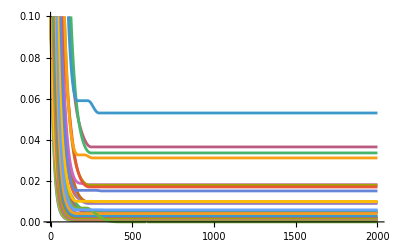

```mathematica
ListPlot[Table[trajectorieson⟦i,All,1⟧⟦1;;⟧,{i,1,Length[trajectorieson],1}],Joined->True,PlotRange->{Automatic,{0,0.1}}]
```